~/OneDrive/Medical Sensor/exp2_data1.xlsx

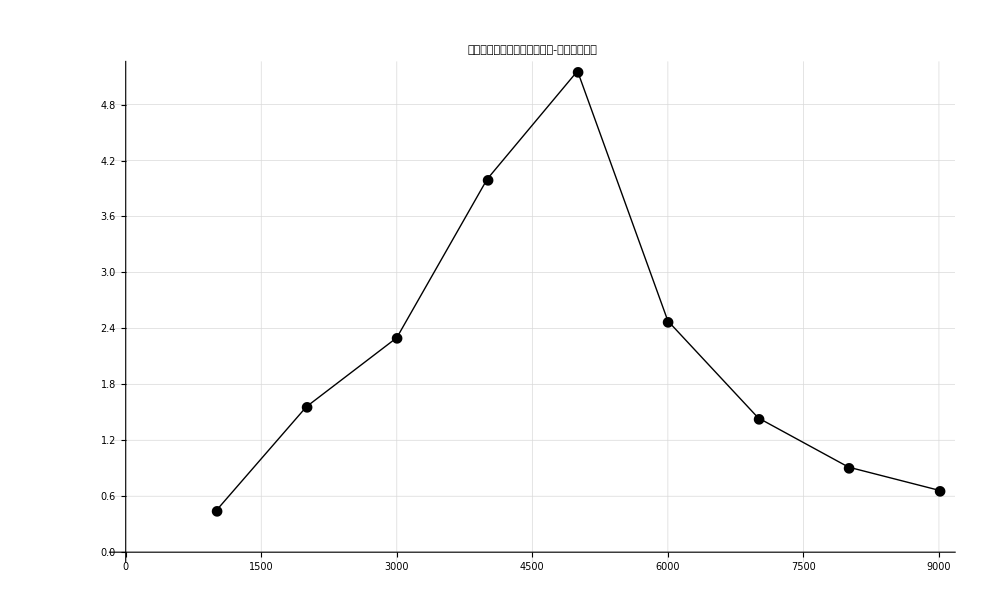

```mathematica
V={0.444,1.56,2.3,4.0,5.16,2.48,1.44,0.912,0.664};
frequency=Range[1000,9000,1000];
coordinates=Transpose[{frequency,V}];
fullFormExp2={frequency,V};
Export["~/OneDrive/Medical Sensor/exp2_data1.xlsx",fullFormExp2,"XLSX"]
PlotGraph=ListLinePlot[
coordinates,
PlotMarkers->{Automatic,14},
PlotStyle->Black,
GridLines->Automatic,
GridLinesStyle->Directive[Black,Dashed],
Frame->Automatic,
FrameLabel->{"f/Hz","V_(op - p)/mV"},
PlotLabel->"不同激励频率下输出电压（峰-峰值）的关系",
BaseStyle->{FontWeight->"Bold",FontSize->18}
]
```

~/OneDrive/Medical Sensor/exp2_data2.xlsx

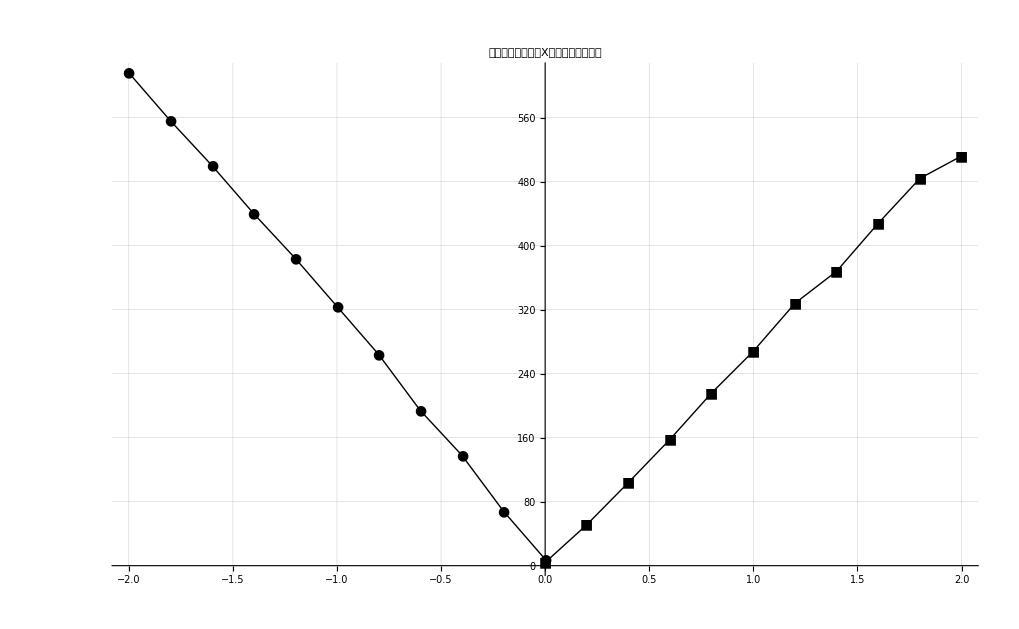

```mathematica
Vminus={616,556,500,440,384,324,264,194,138,68,8};
Vplus={4,51.2,104,158,216,268,328,368,428,484,512};
Xminus=Range[-2,0,0.2];
Xplus=Range[0,2,0.2];
coordinatesMinus=Transpose[{Xminus,Vminus}];
coordinatesPlus=Transpose[{Xplus,Vplus}];
fullFormExp2={Xminus,Vminus,Xplus,Vplus};
Export["~/OneDrive/Medical Sensor/exp2_data2.xlsx",fullFormExp2,"XLSX"]
PlotGraph=ListLinePlot[
{coordinatesMinus,coordinatesPlus},
PlotMarkers->{Automatic,14},
PlotStyle->Black,
GridLines->Automatic,
GridLinesStyle->Directive[Black,Dashed],
Frame->Automatic,
FrameLabel->{"X/mm","V_(op - p)/mV"},
PlotLabel->"差动变压器位移（X）与输出电压关系",
BaseStyle->{FontWeight->"Bold",FontSize->18}
]
```

```mathematica
?Join
```

RowBox[{"Join", "[", RowBox[{SubscriptBox[StyleBox["list", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["list", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] concatenates lists or other expressions that share the same head.
RowBox[{"Join", "[", RowBox[{SubscriptBox[StyleBox["list", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["list", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"], ",", StyleBox["n", "TI"]}], "]"}] joins the objects at level StyleBox["n", "TI"] in each of the SubscriptBox[StyleBox["list", "TI"], StyleBox["i", "TI"]].